## Triangle

```mathematica
ruleTriangleBoundary[matrix_]:=Module[{m=matrix,neighbours,a=Floor[Dimensions[matrix][[1]]/3]},neighbours=ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},ArrayPad[m,1]];
m=ReplacePart[m,Position[neighbours,_?(#<2||#>3&)]->0];
m=ReplacePart[m,Position[neighbours,3]->1];
m=ReplacePart[m,{a,i_}-> -1];
m=ReplacePart[m,Thread[Table[{i+a,i},{i,1,Length@m/2}]->-1]];
m=ReplacePart[m,Thread[Table[{i+a+1,Length[m]-i},{i,0,Length@m/2-1}]->-1]]
]
```

```mathematica
m=ArrayPad[RandomInteger[1,{10,10}],15];
```

```mathematica
ltriangle=ArrayPlot[#,Mesh->True,ColorRules->{1-> Black,0-> White,-1-> Red}]&/@NestList[ruleTriangleBoundary,m,100];
Manipulate[ltriangle[[n]],{n,1,50,1},ImageMargins->32,FrameMargins->30,ContentSize->Large]
```

## Other Values

```mathematica
ruleTriangleBoundarynew[matrix_]:=Module[{m=matrix,neighbours,a=Floor[Dimensions[matrix][[1]]/3]},neighbours=ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},ArrayPad[m,1]];
m=ReplacePart[m,Position[neighbours,_?(#<2||#>3&)]->0];
m=ReplacePart[m,Position[neighbours,3]->1];
m=ReplacePart[m,{a,i_}-> 2];
m=ReplacePart[m,Thread[Table[{i+a,i},{i,1,Length@m/2}]->2]];
m=ReplacePart[m,Thread[Table[{i+a+1,Length[m]-i},{i,0,Length@m/2}]->2]]
]
```

```mathematica
m=ArrayPad[RandomInteger[1,{9,9}],10];
ltriangle=ArrayPlot[#,Mesh->True,ColorRules->{1-> Black,0-> White,-1-> Red,2-> Purple}]&/@NestList[ruleTriangleBoundarynew,m,100];
ListAnimate[ltriangle]
```

## Arbitrary Image

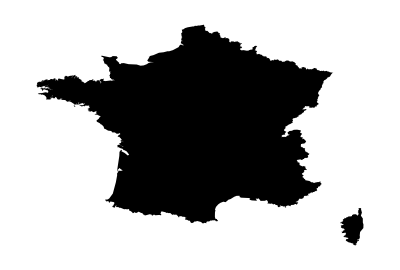

```mathematica
image=Graphics[Entity["Country","France"]["Polygon"]]
```

```mathematica
newimage=ColorNegate[EdgeDetect[ImageResize[image,{86}]]];
matrix=ImageData[newimage];
matrix=Replace[matrix,{0->1,1->0},∞];
boundary=Thread[Position[matrix,1]->-1];
```

```mathematica
dim=Dimensions[matrix];
g=3/4;f=1/4;h=1/2;
mtest=SparseArray[{},{dim⟦1⟧,dim⟦2⟧}];
mtest⟦dim⟦1⟧-Floor[dim⟦1⟧ g];;dim⟦1⟧-Floor[dim⟦1⟧ f],dim⟦2⟧-Floor[dim⟦2⟧ g];;dim⟦2⟧-Floor[dim⟦2⟧ f]⟧=RandomInteger[1,{Ceiling[dim⟦1⟧ h]+1,Ceiling[dim⟦2⟧ h]+1}];
```

```mathematica
randomImage[matrix_]:=Module[{m=matrix,neighbours},neighbours=ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},ArrayPad[m,1]];m=ReplacePart[m,Position[neighbours,_?(#1<2||#1>3&)]->0];m=ReplacePart[m,Position[neighbours,3]->1];m=ReplacePart[m,boundary]
]
```

```mathematica
(*Set of Array Plots with timesteps and Manipulate function for displaying*)
limage=ArrayPlot[#,ColorRules->{1-> Black,0-> White,-1-> Red},ImageSize->Large]&/@
NestList[randomImage,mtest,100];
Manipulate[limage[[n]],{n,3,100,1},ImageMargins->20,FrameMargins->20,ContentSize->Medium,SaveDefinitions->True]
```

## Hexagon

```mathematica
ruleHexagonalBoundary[matrix_]:=Module[{m=matrix,neighbours,l=Dimensions[matrix][[1]],a=0,s=0,e=0},
a=Ceiling[l/6];
s=Floor[l/3];
e=Floor[l*2/3];neighbours=ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},ArrayPad[m,1]];
m=ReplacePart[m,Position[neighbours,_?(#<2||#>3&)]->0];
m=ReplacePart[m,Position[neighbours,3]->1];
m=ReplacePart[m,Table[{a+1,i+1},{i,s,e}]->-1];(*top*)
m=ReplacePart[m,Table[{e+a,i+1},{i,s,e}]->-1];(*bottom*)
m=ReplacePart[m,Thread[Table[{i+a,i+e},{i,1,l}]->-1]];(*uprigth*)
m=ReplacePart[m,Thread[Table[{i+s+1+a,Length[m]-i},{i,0,s}]->-1]];(*drigth*)
m=ReplacePart[m,Thread[Table[{i+a,Length[m]-i-e+1},{i,1,s}]->-1]];(*upleft*)
m=ReplacePart[m,Thread[Table[{i+a+s,i},{i,1,s}]->-1]]
]
```

```mathematica
lhexagon=ArrayPlot[#,Mesh->True,ColorRules->{1-> Black,0-> White,-1-> Red}]&/@NestList[ruleHexagonalBoundary,m,100];
Manipulate[lhexagon[[n]],{n,1,100,1},ImageMargins->32,FrameMargins->30,ContentSize->Large]
```

## Rules Combined

```mathematica
rulescombined[matrix_]:=Module[{m=matrix,neighbours,a=Floor[Dimensions[matrix][[1]]/4],l=Max[Dimensions[matrix]]},neighbours=ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},ArrayPad[m,1]];m=ReplacePart[m,Position[neighbours,_?(#1<2||#1>3&)]->0];m=ReplacePart[m,Position[neighbours,3]->1];m=ReplacePart[m,boundary];
m=ReplacePart[m,Table[{a,i},{i,1,l}]-> 2];
m=ReplacePart[m,Thread[Table[{i+a,i},{i,1,l/2}]->2]];
m=ReplacePart[m,Thread[Table[{i+a+1,l-i},{i,0,l/2}]->2]]
]
```

```mathematica
(*Set of Array Plots with timesteps and Manipulate function for displaying*)
l1image=ArrayPlot[#,ColorRules->{1-> Black,0-> White,-1-> Red,2->Purple},ImageSize->Large]&/@
NestList[rulescombined,mtest,100];
Manipulate[l1image[[n]],{n,1,100,1},ImageMargins->20,FrameMargins->20,ContentSize->Medium,SaveDefinitions->True]
```